```mathematica
观察误差积累
```

E = 0.0726 eV

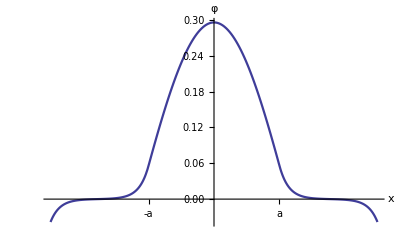

```mathematica
ξ=1.37915;a=10;V0=2;energy=3.81511×10^-2 ξ^2;Print["E = ",SetPrecision[energy,3]," eV"]
U[x_]:=If[Abs[x]≤a,0,V0];x0=2.5a;
β[x_]:=0.262116*(U[x]-energy);
s=NDSolve[{φ''[x]-β[x]*φ[x]==0,φ[0]==10,
φ'[0]==0},φ,{x,-x0,x0}];
ma=NIntegrate[φ[x]^2/.First[s],
{x,-x0,x0}];
Plot[(φ[x]/.First[s])/√ma,{x,-x0,x0},
PlotRange->All,PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
Ticks->{{{-a,"-a"},{a,"a"}},Automatic},
PlotPoints->200,AxesLabel->{"x","φ"}]
Clear[ξ,a,V0,energy,U,β,s,ma,φ]
```